```mathematica
randpoint:=With[{x=RandomReal[],r=Sqrt[3]},{x,RandomReal[]*Min[r*x,r*(1-x)]}]
```

```mathematica
nextPoint[np_,start_]:=With[{i=RandomReal[]*Length[start]+1//Floor},
.5*(np+start[[i]])]
```

```mathematica
iterate[n_,start_]:=start~Join~NestList[nextPoint[#,start]&,randpoint,n]
```

```mathematica
drawN[n_]:=With[{startpoints={{0,0},{0.5,Sqrt[3]/2},{1,0}}},
ListPlot[iterate[n,startpoints],Axes->False,AspectRatio->1]]
```

```mathematica
regularNgon[n_]:=With[{angle=2*Pi/n},
Table[{Cos[k*angle],Sin[k*angle]},{k,0,n-1}]]
```

```mathematica
drawN[n_,k_]:=With[{startpoints=regularNgon[k]},
ListPlot[iterate[n,startpoints],Axes->False,AspectRatio->1]]
```

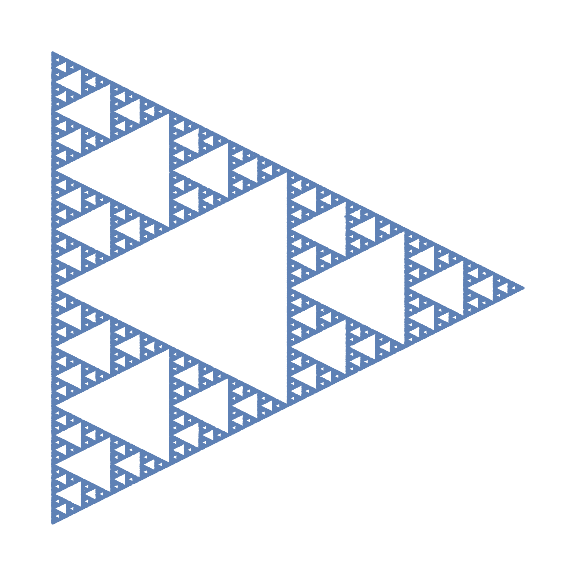

```mathematica
drawN[100000,3]
```